```mathematica
(*This notebook creates the figures for the cjSOE model using ctDiscrete code*)
```

```mathematica
ClearAll["Global`*"];ParamsAreSet=False;
(* If running from the Notebook interface *)
If[$VersionNumber<8,(*then*) Print["These programs require Mathematica version 8 or greater."];Abort[]];

If[Length[$FrontEnd] > 0,NBDir=SetDirectory[NotebookDirectory[]]];(* If running from the Notebook interface *)
If[$FrontEnd == Null,OpenFigsUsingShell=True,OpenFigsUsingShell=False]; 
AutoLoadDir=SetDirectory["../../CoreCode/Autoload"];Get["./init.m"];
CoreCodeDir=SetDirectory[".."];
rootDir = SetDirectory[".."];(* root directory is above CoreCode *)
FigsDir=SetDirectory[rootDir<>"/Examples/cjSOE/Figures/"];
CodeDir=SetDirectory[rootDir<>"/Examples/cjSOE"];
Get[CoreCodeDir<>"/MakeAnalyticalResults.m"];
Get[CoreCodeDir<>"/VarsAndFuncs.m"];
(* Method of creating figures depends on whether being run in batch mode or interactively *)
If[$FrontEnd == Null,OpenFigsUsingShell=True,OpenFigsUsingShell=False]; 
(* Get[CoreCodeDir<>"/ParametersBase.m"]; *)
```

```mathematica
Get[CodeDir<>"/FuncsInit.m"];
Get[CodeDir<>"/FuncsSOE.m"];
Get[CodeDir<>"/FuncsIndivProblem.m"];
```

```mathematica
(* Derivations from equations in the cjSOE paper *)
(* 𝒷 is idiosyncratic, ℬ is aggregate *)
(* TargTarg and ws are both markers for the model "with stakes" *)
(* E signifies for the Employed consumer and U signifies the Unemployed *)
𝒷TargTarg = 1/(PGro/R-1/(2-LGro)+κ (1+(ÞΓ^-ρ-1)/℧)^(1/ρ));(* Equation bTargEStakes *)
ℬEws=(1-kapshare)𝒷TargTarg ;(* Equation BRatEStakes *)
ℬUws=((℧ EmpGro WGro)/(EmpGro WGro - PLives Þ))ℬEws;(* Equation BuOyLev*)
ℬTotws=ℬEws+ℬUws; (* Total ℬ is the sum of that for the employed and unemployed *)
```

```mathematica
(* Algebra to obtain the function in terms of primitives *)
{{ℬws == ℬUws+ℬEws},
{ℬws == (((℧ EmpGro WGro)/(EmpGro WGro - PLives Þ))+1)ℬEws},
{ℬws == (((℧ EmpGro WGro)/(EmpGro WGro - PLives Þ))+1)(1-kapshare)𝒷TargTarg },
{ℬws == (((℧ EmpGro WGro)/(EmpGro WGro - PLives Þ))+1)(1-kapshare)1/(PGro/R-1/(2-LGro)+κ (1+(ÞΓ^-ρ-1)/℧)^(1/ρ)) },
{ℬws ==( ((℧ EmpGro PGro)/(EmpGro PGro - PLives Þ))+(1-kapshare))1/(PGro/R-1/(2-LGro)+κ (1+(ÞΓ^-ρ-1)/℧)^(1/ρ)) }
};
```

```mathematica
(* Define it as a function directly *)
ℬwsFunc[℧Val_]:= (((℧Val EmpGro WGro)/(EmpGro WGro - PLives Þ))+1)(1-kapshare)1/(PGro/R-1/(2-LGro)+κ (1+(ÞΓ^-ρ-1)/(℧Val))^(1/ρ)) ;
```

```mathematica
(* Now instantiate parameter values *)
resetParams;
calculateValues;
```

```mathematica
cstwMPCKtoYTargetQtr=10.26; (* The cstwMPC model's B/Y ratio (quarterly) *)
cstwMPCKtoYTargetAnn=cstwMPCKtoYTargetQtr/4; (* A year has 4 quarters *)
(* Calculate the value of ℧ that generates the target ratio *)
℧MatchesB=(℧Val /. FindRoot[ℬwsFunc[℧Val] == cstwMPCKtoYTargetAnn,{℧Val,0.001,0.13}][[1]])
```

0.0116577

```mathematica
ζTractable=(ℬwsFunc[℧MatchesB]-ℬwsFunc[0.5 ℧MatchesB])/(0.5 ℧MatchesB)
```

128.449

```mathematica
ℬwsFunc[0.5 ℧MatchesB]/ℬwsFunc[℧MatchesB]
```

0.708105

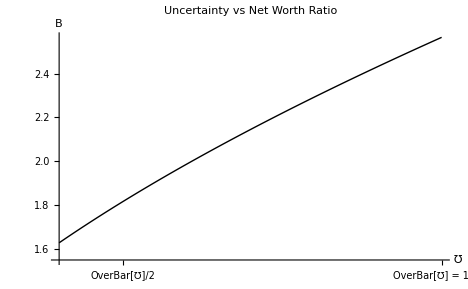

/Volumes/Data/Code/Models/Tractable/Latest/EqbmGeneral/Mathematica/Examples/cjSOE/Figures/BvsMho.png

```mathematica
BvsMhoFig=Plot[ℬwsFunc[℧Val],{℧Val,0.4 ℧MatchesB,1.0 ℧MatchesB}
,PlotLabel->"Uncertainty vs Net Worth Ratio",
AxesLabel->{"℧","B"},
AxesOrigin-> {Automatic,{1.55,Automatic}},
PlotRange->{Automatic,{1.55,Automatic}},
Ticks->{{{℧MatchesB/2,"OverBar[℧^]/2"},{℧MatchesB,"OverBar[℧^] = 1.012"}},Automatic}];
Print[BvsMhoFig];
Export[FigsDir<>"/"<>"BvsMho.pdf",BvsMhoFig];
Export[FigsDir<>"/"<>"BvsMho.png",BvsMhoFig,ImageSize->FullPageSize]
```